```mathematica
randomPointSphericalCap[αMax_]:=Module[{phi =8 ArcSin[Sqrt[RandomReal[{0,1}]]Sin[αMax/8]],r},
r = Sin[phi/4];
Flatten[{Cos[phi/4],r AngleVector[RandomReal[{0,2Pi}]]}]
]
```

```mathematica
randomPointSphericalCap[αMax_,n_]:=Module[{phi =8 ArcSin[Sqrt[RandomReal[{0,1},n]]Sin[αMax/8]],r},
r = Sin[phi/4];
MapThread[
Flatten[{#3,#1 AngleVector[#2]}]&,{r,RandomReal[{0,2Pi},n],Cos[phi/4]}]
]
```

```mathematica
randomPointSphericalCapRotationMatrix[αMax_,n_]:=
Map[
RotationMatrix[{{1,0,0},#}]&,
randomPointSphericalCap[αMax,n]
]
```

```mathematica
randomCorrelatedWalk[units_, α_]:= 
With[{rotations = 
randomPointSphericalCapRotationMatrix[α,units]},
Accumulate[(FoldList[Dot[#1,#2]&,rotations][[All,All,1]])]
]
```

```mathematica
randomCorrelatedDisplacement[units_, α_]:= 
With[{rotations = 
randomPointSphericalCapRotationMatrix[α,units]},
Norm[Total[(FoldList[Dot[#1,#2]&,rotations][[All,All,1]])]]
]
```

```mathematica
AbsoluteTiming[randomCorrelatedWalk[2^17, Pi/2];]
```

{21.1126,Null}

```mathematica
41 18 1000/60/60/24.
```

8.54167

```mathematica
AbsoluteTiming[
With[{monteCarloExperiments =1000, nExponent=18},
correlatedRandomWalkData =
Join[<|"Monte Carlo Experiments"->monteCarloExperiments|>, Association[
ParallelTable[Print[{α, DateString[]}];
<|α->
With[{walkExperiments =
Table[randomCorrelatedWalk[2^nExponent, α],monteCarloExperiments]
},
Association@Table[
2^n-><|
"Mean"->Mean[Norm/@walkExperiments[[All,2^n]]],"Standard Deviation"-> StandardDeviation[Norm/@walkExperiments[[All,2^n]]],
"Mean Direction"->Mean[walkExperiments[[All,2^n]]-walkExperiments[[All,2^n -1]]] |>,{n,2,nExponent}]
]|>,
{α,Pi/6,4Pi,Pi/6}
]
]
];
]
]
```

{π/6,Fri 28 Jan 2022 11:52:09}

{(2 π)/3,Fri 28 Jan 2022 11:52:09}

{(7 π)/6,Fri 28 Jan 2022 11:52:09}

{(5 π)/3,Fri 28 Jan 2022 11:52:09}

{(13 π)/6,Fri 28 Jan 2022 11:52:09}

{(8 π)/3,Fri 28 Jan 2022 11:52:09}

{(19 π)/6,Fri 28 Jan 2022 11:52:09}

{(11 π)/3,Fri 28 Jan 2022 11:52:09}

$Aborted

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"correlatedRandomWalkData_n=1000_exp=18.mx"}],correlatedRandomWalkData]
```

{0.076241,Null}

```mathematica
correlatedRandomWalkData
```

```mathematica
correlatedRandomWalkData[Pi][[All,"Mean"]]
```

<|4→3.55454,8→6.12095,16→8.47167,32→15.6904,64→27.2448|>

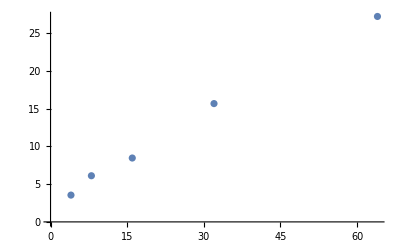

```mathematica
ListPlot[correlatedRandomWalkData[Pi][[All,"Mean"]]]
```